```mathematica
Mark6 Disk Performance Results
```

## Introduction

This document describes the individual disk performance results for disks in Mark6 disk packs mk6 + 005, mk6 + 006, mk6 + 007, mk6 + 008, mk6 + 009. The results were measured using the FIO linux benchmarking program.

## External Libraries

```mathematica
Needs["ComputerArithmetic`"];
Needs["PlotLegends`"];
```

## Import Data

```mathematica
SetDirectory["/opt/src/mark6/tests/disk"];
nrDirectories={"mk6+005","mk6+006","mk6+007","mk6+008", "gsfc+001", "gsfc+002"};
(* mk6006, mk6007, mk6008 *)
nrFiles=FileNames[#<>"/disk*.log"]&/@nrDirectories

windowSize=120;
rawData=Function[files,
Function[file,
data=Import[file,"CSV"][[All,{1,2}]];
time=data[[All,1]]/1000;
averageData=MovingAverage[8/1000 data[[All,2]],windowSize];
Partition[Riffle[time,averageData],2]
]/@files
]/@nrFiles;

mk6005Data=rawData[[1]];
Length[mk6005Data]

mk6006Data=rawData[[2]];
Length[mk6006Data]

mk6007Data=rawData[[3]];
Length[mk6007Data]

mk6008Data=rawData[[4]];
Length[mk6008Data]

(* Goddard Data *)
gsfc001Data=rawData[[5]];
gsfc002Data=rawData[[6]];
```

8

8

8

«1 more identical outputs»

## Serial Numbers

```mathematica
mk6007Serials={
"WD-WCATR5882337",
"WD-WCATR5842519",
"WD-WCATR5842024",
"WD-WCATR5854063",
"WD-WCATR5842518",
"WD-WCATR5873146",
"WD-WCATR5854139",
"WD-WCATR5873160"
};

mk6008Serials={
"WD-WCATR5862117",
	"WD-WCATR5836481",
	"WD-WCATR5861698",
	"WD-WCATR5841686",
	"WD-WCATR5861912",
	"WD-WCATR5882097",
	"WD-WCATR5879679",
	"WD-WCATR5879319"
};

mk6005Serials={
	"WD-WCATR5882572",
	"WD-WCATR5862262",
	"WD-WCATR5861552",
	"WD-WCATR5879674",
	"WD-WCATR5873892",
	"WD-WCATR5861375",
	"WD-WCATR5879596",
	"WD-WCATR5884830"
};

mk6006Serials={
"WD-WCATR5861771",
"WD-WCATR5862741",
"WD-WCATR5880404",
"WD-WCATR5880028",
"WD-WCATR5870986",
"WD-WCATR5882830",
"WD-WCATR5880218",
"WD-WCATR5870859"
};

mk6009Serials={
"WD-WMAY01837808",
"WD-WMAY02074904",
"WD-WMAY02074917",
"WD-WMAY01790329",
"WD-WMAY02074892",
"WD-WMAY01548353",
"WD-WMAY02041851",
"WD-WMAY01299169"
};

gsfc001Serials={
"RAID0-1",
"RAID0-2",
"RAID0-3",
"RAID0-4"
};
```

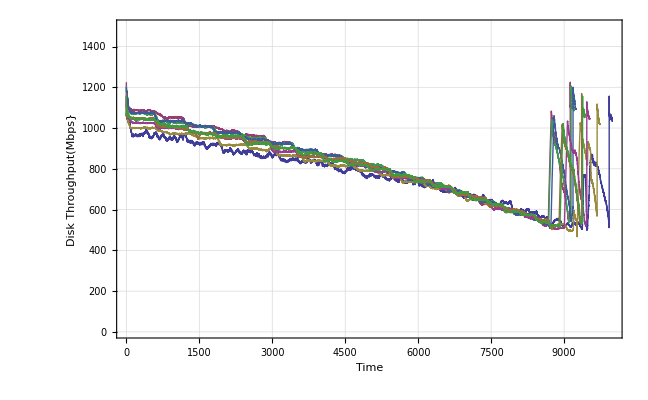

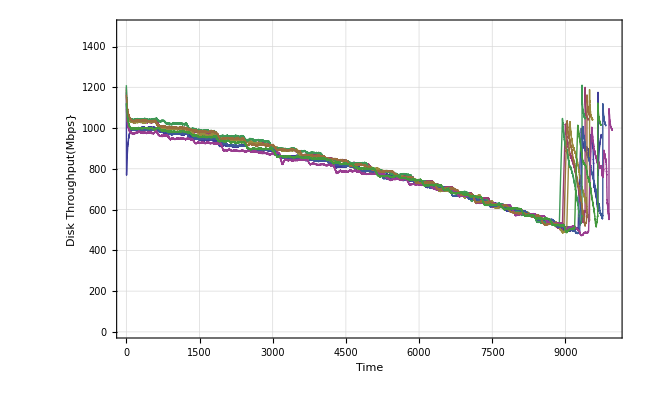

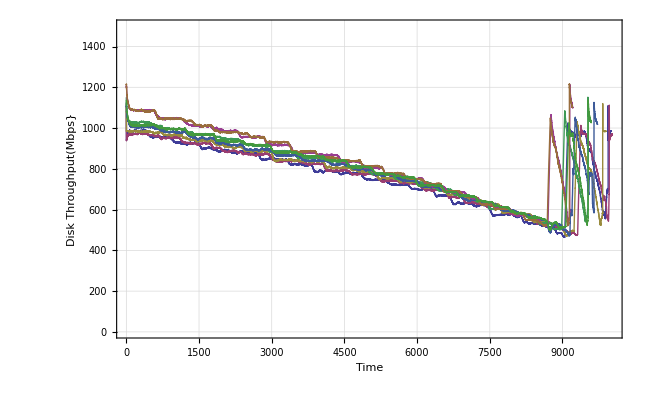

```mathematica
ListPlot[mk6005Data,{Joined->True,PlotRange->{All,{0,1500}},ImageSize->{72 9, 72 6},Frame->True,FrameLabel->{"Time", "Disk Throughput(Mbps}", " Individual Disk Throughput",""},GridLines->Automatic ,PlotLegend->mk6005Serials,LegendShadow->False,LegendPosition->{1.1,-0.4},LegendSize->{0.9,0.8}}]
ListPlot[mk6006Data,{Joined->True,PlotRange->{All,{0,1500}},ImageSize->{72 9, 72 6},Frame->True,FrameLabel->{"Time", "Disk Throughput(Mbps}", " Individual Disk Throughput",""},GridLines->Automatic ,PlotLegend->mk6006Serials,LegendShadow->False,LegendPosition->{1.1,-0.4},LegendSize->{0.9,0.8}}]
ListPlot[mk6007Data,{Joined->True,PlotRange->{All,{0,1500}},ImageSize->{72 9, 72 6},Frame->True,FrameLabel->{"Time", "Disk Throughput(Mbps}", " Individual Disk Throughput",""},GridLines->Automatic ,PlotLegend->mk6007Serials,LegendShadow->False,LegendPosition->{1.1,-0.4},LegendSize->{0.9,0.8}}]
ListPlot[mk6008Data,{Joined->True,PlotRange->{All,{0,1500}},ImageSize->{72 9, 72 6},Frame->True,FrameLabel->{"Time", "Disk Throughput(Mbps}", " Individual Disk Throughput",""},GridLines->Automatic ,PlotLegend->mk6008Serials,LegendShadow->False,LegendPosition->{1.1,-0.4},LegendSize->{0.9,0.8}}]
```

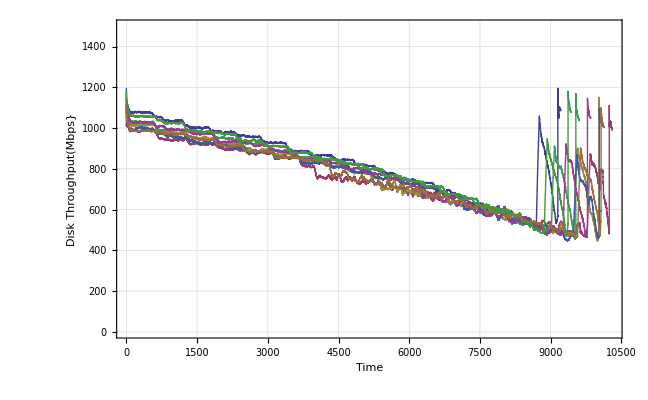

## GSFC RAID0 Modules

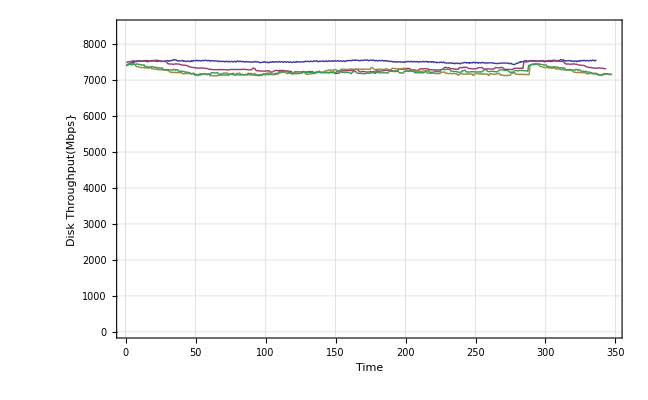

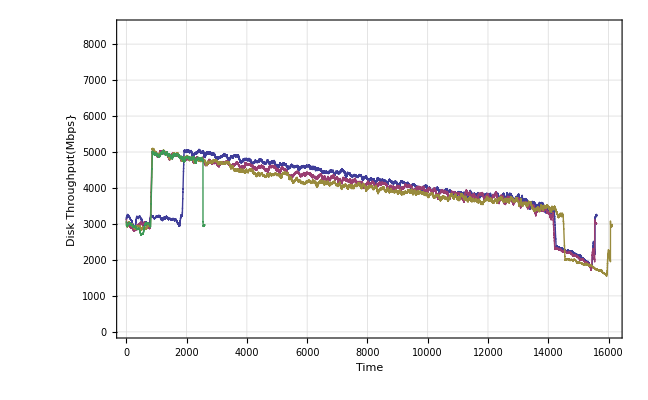

```mathematica
gsfcPlot=ListPlot[gsfc001Data,{Joined->True,PlotRange->{All,{0,8500}},ImageSize->{72 9, 72 6},Frame->True,FrameLabel->{"Time", "Disk Throughput(Mbps}", " Aggregated RAID0  Throughput (FC13)",""},GridLines->Automatic ,PlotLegend->gsfc001Serials,LegendShadow->False,LegendPosition->{1.1,-0.4},LegendSize->{0.9,0.8}}]
Export["gsfc_raid0_module_throughput(fc).png",gsfcPlot];
gsfcPlot=ListPlot[gsfc002Data,{Joined->True,PlotRange->{All,{0,8500}},ImageSize->{72 9, 72 6},Frame->True,FrameLabel->{"Time", "Disk Throughput(Mbps}", " Aggregated RAID0  Throughput (DEB6.02)",""},GridLines->Automatic ,PlotLegend->gsfc001Serials,LegendShadow->False,LegendPosition->{1.1,-0.4},LegendSize->{0.9,0.8}}]
Export["gsfc_raid0_module_throughput(deb).png",gsfcPlot];
```